## Initialization Notation

```mathematica
Unprotect["Global`*"]
Clear["Global`*"]
ClearAll["Global`*"] 
Remove["Global`*"] 
Unprotect[Out];
$HistoryLength=0;
ParallelEvaluate[$HistoryLength=0];
<<Notation`
Off[Symbolize::bsymbexs]
Off[Remove::rmnsm]
Print["Variable Cleared"]
(*AutoCollapse[]*)
```

{}

Variable Cleared

```mathematica
Symbolize[(U⃗)_n];Symbolize[(X⃗)_r];Symbolize[(U⃗)^n];Symbolize[X⃗];Symbolize[τ^n];
Symbolize[L̄];Symbolize[x_^h];Symbolize[x_^e];Symbolize[Ε^*];Symbolize[Subscript[n, x_]];
Symbolize[Subscript[x_, i_]];Symbolize[(x⃗)^h];Symbolize[OverHat[x_]];Symbolize[x̲];
Print["New Symbols Defined"]
(*AutoCollapse[]*)
```

New Symbols Defined

```mathematica
<<HaneeshPackages`
PrntRls={Subscript[u, 1]-> Subscript[u,1],Subscript[u, 2]-> Subscript[u,2],Subscript[u, 3]-> Subscript[u,3],
Subscript[x, 1]-> Subscript[x,1],Subscript[x, 2]-> Subscript[x,2],Subscript[x, 3]-> Subscript[x,3],
u^ρ-> Superscript[u,ρ],u^ϕ-> Superscript[u,ϕ],u^ζ-> Superscript[u,ζ],
Subscript[u, ρ]-> Subscript[u,ρ],Subscript[u, ϕ]-> Subscript[u,ϕ],Subscript[u, ζ]-> Subscript[u,ζ],
N^𝔄-> Superscript[N,𝔄],N^𝔅-> Superscript[N,𝔅],N^ℭ-> Superscript[N,ℭ],
N^𝔇-> Superscript[N,𝔇],N^𝔈-> Superscript[N,𝔈],N^𝔉-> Superscript[N,𝔉],N^(a)-> Superscript[N,"(a)"],N^(b)-> Superscript[N,"(b)"],
Subscript[a, ρ, 𝔄]-> Subscript[a,ρ,𝔄],Subscript[a, ϕ, 𝔅]-> Subscript[a,ϕ,𝔅],Subscript[a, ζ, ℭ]-> Subscript[a,ζ,ℭ],
Subscript[b, ρ, 𝔇]-> Subscript[b,ρ,𝔇],Subscript[b, ϕ, 𝔈]-> Subscript[b,ϕ,𝔈],Subscript[b, ζ, 𝔉]-> Subscript[b,ζ,𝔉],
Subscript[a, x, 𝔄]-> Subscript[a,x,𝔄],Subscript[a, y, 𝔅]-> Subscript[a,y,𝔅],Subscript[a, z, ℭ]-> Subscript[a,z,ℭ],
Subscript[b, x, 𝔇]-> Subscript[b,x,𝔇],Subscript[b, y, 𝔈]-> Subscript[b,y,𝔈],Subscript[b, z, 𝔉]-> Subscript[b,z,𝔉],
N_(,ζ)^(a)->Subsuperscript[N,",ζ","(a)"],N_(,ρ)^(a)->Subsuperscript[N,",ρ","(a)"],N_(,ζ)^(b)->Subsuperscript[N,",ζ","(b)"],N_(,ρ)^(b)->Subsuperscript[N,",ρ","(b)"],
N_(,x)^(a)->Subsuperscript[N,",x","(a)"],
N_(,y)^(a)->Subsuperscript[N,",y","(a)"],
N_(,z)^(a)->Subsuperscript[N,",z","(a)"],
N_(,x)^(b)->Subsuperscript[N,",x","(b)"],
N_(,y)^(b)->Subsuperscript[N,",y","(b)"],
N_(,z)^(b)->Subsuperscript[N,",z","(b)"],
Subscript[w, ρ]-> Subscript[w,ρ],Subscript[w, ϕ]-> Subscript[w,ϕ],Subscript[w, ζ]-> Subscript[w,ζ],
L̄->Overscript[L,_],Subscript[ΔT, 0]-> Subscript[ΔT,0]
};
GenerateMonoSubSuperscriptRules[]:=Module[{body, ww,zz,xx,yy,Prules1,Prules2,scripts},
body=Join[Alphabet["Greek"],Alphabet[],ToUpperCase[Alphabet[]],ToUpperCase[Alphabet["Greek"]]];
scripts=Join[Table[ToString[i],{i,1,9}],List@ToString[ϕ],Map[ToString,Alphabet["Greek"]]];
xx=Flatten@Outer[StringJoin,Map[ToString,body],{"⎵Subscript⎵"},scripts];
xx=Map[Symbol,xx];
yy=Flatten@Outer[Subscript,body,scripts];
Prules1=Table[xx[[i]]->yy[[i]],{i,1,Length@xx}];
ww=Flatten@Outer[StringJoin,Map[ToString,body],{"⎵Superscript⎵"},scripts];
ww=Map[Symbol,ww];
zz=Flatten@Outer[Superscript,body,scripts];
Prules2=Table[ww[[i]]->zz[[i]],{i,1,Length@xx}];
Join[Prules1,Prules2]]
(*PrntRls=Join[PrntRls,GenerateMonoSubSuperscriptRules[]];*)
Pprint[expri_]:=Module[{expr=expri},
expr/.PrntRls//MatrixForm//pdConv
];
Pprint[expri_,title_]:=Module[{expr=expri},
(title=expr)/.PrntRls//MatrixForm//pdConv
];
Print["Print Subroutines Defined"]
(*AutoCollapse[]*)
```

Print Subroutines Defined

```mathematica
Subscript[u, ρ]::usage="Covariant component of the displacement in the g^ρ direction (symbol)";
Subscript[u, ϕ]::usage="Covariant component of the displacement in the g^ϕ direction ";
Subscript[u, ζ]::usage="Covariant component of the displacement in the g^ζ direction ";

λ::usage="Lame constant (double)";
μ::usage="Lame constant (double)";
Subscript[ρ, 0]::usage="inner radius (double)";
Subscript[ρ, 1]::usage="outer radius (double)";
Subscript[ζ, 0]::usage="curvilinear coordinate ζ's lower bound(double)";
Subscript[ζ, 1]::usage="curvilinear coordinate ζ's upper bound(double)";
αΔT::usage="α=Coefficient of thermal expansion; ΔT=Temperature change function";

Subscript[n, el]::usage="\tNumber of Finite Elements";
Subscript[n, np]::usage="Number of Finite Element Nodes";
Subscript[n, dof]::usage="Number of degrees of freedom per node";
Subscript[n, en]::usage="Number of nodes per finite element";
Subscript[n, eq]::usage="Total Number of Equations";
Subscript[n, guass]:: usage="Number of integration points";
(x⃗)^h::usage="{ρ_A, ζ_A} = (x⃗)^h⟦A⟧\n A = Global node number\n {ρ_A, ζ_A}= Nodal co-ordinates\n Dimensions[(x⃗)^h]= n_npX n_sd ";
Subscript[n, sd]::usage="Number of space dimensions";
(*Data Structure Arrays*)

SetUpIDArray::usage="Call as SetUpIDArray[]. Will return the ID array";
IEN::usage="IEN(a,e) = A\n\n\ta = Local Node Number\n\te = Element Number\n\tA = Global Node Number";
ID::usage="Dimensions[ID]={n_dof,n_np}\n  
ID[i,A]=Piecewise[{{P,, A∈η-η_g}, {0, A∈η-η_g_i}}]
";
<<NDSolve`FEM`
SetDirectory[NotebookDirectory[]];
Print["Nomenclature defined"]
(*AutoCollapse[]*)
```

Nomenclature defined

## Problem Solution: Numerics

### Numerics subroutine:

```mathematica
ApplyBC[𝓉0_]:=Module[{𝓉 = 𝓉0,û,v̂,ŵ,x,Subscript[𝓉, x],Subscript[𝓉, y],Subscript[𝓉, z],normals},
û[x_List]:=0.0;
v̂[x_List]:=  x[[2]]𝓉;
ŵ[x_List]:=0.0;
SetUpDirichletBC[{û,v̂,ŵ}];
Subscript[𝓉, x][x_List]:=0.0;
Subscript[𝓉, y][x_List]:= 0.0;
Subscript[𝓉, z][x_List]:=0.0;
SetUpNeumannBC[{Subscript[𝓉, x],Subscript[𝓉, y],Subscript[𝓉, z]}];
normals=(Ω^h)["BoundaryNormals"][[1]];
Edges =Extract[(Ω^h)["BoundaryElements"][[1,1]],Position[Map[Norm@(#-{0,1})&,normals],x_/;x<10^-5]];
];
SetUpDirichletBC[Funcs_List]:=Module[{BCVals,Nodes1,Nodes2,Nodes,Nodes3,Nodes4,NodesZ
,tol=10^-5
,Subscript[x, 0]=0.0
,Subscript[y, 0]=0.0
,Subscript[x, 1]=1.0
,Subscript[y, 1]=1.0
,Subscript[z, 1]=1.0},
Nodes1 =Flatten@Position[Abs[((x⃗)^h)[[;;,2]]-Subscript[y, 0]],x_/;x<tol];
Nodes2 =Flatten@Position[Abs[((x⃗)^h)[[;;,2]]-Subscript[y, 1]],x_/;x<tol];
Nodes4= Flatten@Position[Abs[((x⃗)^h)[[;;,1]]-Subscript[x, 0]],x_/;x<tol];
Nodes = Join[{2,#}&/@Nodes1,{2,#}&/@Nodes2,{1,#}&/@Nodes4];
If[Subscript[n, dof]==3,
NodesZ=Flatten@Position[Abs[((x⃗)^h)[[;;,3]]-Subscript[z, 1]],x_/;x<tol];
Nodes = Join[Nodes,{3,#}&/@NodesZ];
];
BCVals=Funcs[[#[[1]]]][((x⃗)^h)[[#[[2]]]]]&/@Nodes;
DirichletDof = Sort[(Nodes[[;;,2]]-1)*Subscript[n, dof]+Nodes[[;;,1]]];
DirichletNode=AssociationThread[Nodes->BCVals];
];
SetUpNeumannBC[Funcs_List]:=Module[{BCVals,Nodes1,Nodes2,Nodes,Nodes3,Nodes4
,tol=10^-5
,Subscript[x, 1]=1.0
,Subscript[y, 0]=0.0
,Subscript[y, 1]=L},
Nodes1=Flatten@Position[Abs[((x⃗)^h)[[;;,1]]-Subscript[x, 1]],x_/;x<tol];
(*Nodes2=Flatten@Position[Abs[(x⃗)^h[[;;,2]]-Subscript[y, 1]],x_/;x<tol];*)
(*Nodes =  Join[{2,#}&/@Nodes1,{2,#}&/@Nodes2];*)
Nodes =  {1,#}&/@Nodes1;
BCVals=Funcs[[#[[1]]]][((x⃗)^h)[[#[[2]]]]]&/@Nodes;
NeumannBC=AssociationThread[Nodes->BCVals];
];
```

```mathematica
DefineGaussAndSFInfo[ElementType_,integrationOrder_,elementOrder_]:=
Module[{},
GuassPointsNatural=ElementIntegrationPoints[ToExpression[ElementType],integrationOrder];
GuassWeights=ElementIntegrationWeights[ToExpression[ElementType],integrationOrder];
Subscript[n, guass]=GuassWeights//Length;
NMat=ElementShapeFunction[ToExpression[ElementType],elementOrder];
dN= ElementShapeFunctionDerivative[ToExpression[ElementType],elementOrder];
];
GuassIntegrate[coord_List,f0_]:=Module[{f=f0,GuassPointsSpatial},
GuassPointsSpatial=Apply[NMat,GuassPointsNatural,2].coord;
GuassWeights.MapThread[f,{GuassPointsNatural,GuassPointsSpatial}]
];
```

```mathematica
ComputeStiffnessMatrixU[e0_]:=Module[{e=e0,B,Q,j^e,B^e,k^e,ℐk,coord},
B=IEN[[;;,e]];
coord=((x⃗)^h)[[B]];
j^e=Det@((dN@@#).coord)&;
B^e=(Inverse[(dN@@#).coord].dN@@#)&;
Q=Flatten@IDMat[[;;,B]];
k^e=(j^e)[#]Transpose[(B^e)[#]].StiffnessContra.(B^e)[#]&;
ℐk=Flatten[GuassIntegrate[coord,k^e],{{2,1},{3,4}}];
KMat[[Q,Q]]+=ℐk;
Remove[e,B,Q,j^e,B^e,k^e,ℐk,coord];
]
ComputeResidualMatrixU[e0_]:=Module[{e=e0,B,Q,j^e,B^e,f^e,r^e,d^e,ℐr,TransPu^e,coord},
B=IEN[[;;,e]];
coord=((x⃗)^h)[[B]];
j^e=Det@((dN@@#).coord)&;
B^e=(Inverse[(dN@@#).coord].dN@@#)&;
Q=Flatten@IDMat[[;;,B]];
TransPu^e=Transpose[UMat[[;;,B]]];
f^e=-(j^e)[#1](3 λ+2 μ) αΔT[#2](B^e)[#1]&;
r^e=(j^e)[#]TensorContract[StiffnessContra.((B^e)[#].TransPu^e),{3,4}].(B^e)[#]&;
d^e=(f^e)[#1,#2]-(r^e)[#1]&;
ℐr= Flatten@GuassIntegrate[coord,d^e];
rMat[[Q]]+=ℐr;
Remove[e,B,Q,j^e,B^e,f^e,r^e,d^e,ℐr,TransPu^e,coord];
]
```

```mathematica
ApplyTraction[Edge_]:=
Module[{OutEdge,CoordLine,Jacobi,EquivalentTractionVector,Q},
OutEdge=Flatten[Outer[List,{1,2},Edge],1];
CoordLine =((x⃗)^h)[[Edge]];
Jacobi =Norm[Subtract@@CoordLine]/2 ;
EquivalentTractionVector=
Jacobi*ReplacePart[Map[NeumannBC,OutEdge],Position[KeyExistsQ[NeumannBC,#]&/@OutEdge,False]->0.0];
Q=Flatten@IDMat[[;;,Edge]];
rMat[[Q]]+=EquivalentTractionVector;
Remove[OutEdge,CoordLine,Jacobi,EquivalentTractionVector,Q];
]
```

```mathematica
PlotMeshBC[OptionsPattern[]]:=Module[{DirichletPoints,plt},
Switch[OptionValue[ShowBCs]
,"DirichletBC"
,DirichletPoints =Cases[Keys[DirichletNode],{#,_}][[;;,2]]&/@Range[Subscript[n, dof]];
plt = True;
,"NeumannBC"
,DirichletPoints =Cases[Keys[NeumannBC],{#,_}][[;;,2]]&/@Range[Subscript[n, dof]];
plt = True;
,False
,plt =False;];
Show[
Join[{(Ω^h)["Wireframe"]}
,
If[OptionValue[ShowNumbers]
,{(Ω^h)["Wireframe"["MeshElement" -> "MeshElements","MeshElementIDStyle"->Blue]]
,(Ω^h)["Wireframe"["MeshElement" -> "PointElements","MeshElementIDStyle"->Red]]},{}]
,
If[plt
,Switch[Subscript[n, dof]
,2,{Graphics[{PointSize[Large],Orange,Point[((x⃗)^h)[[DirichletPoints[[1]]]]]}]
,Graphics[{PointSize[Large],Green,Point[((x⃗)^h)[[DirichletPoints[[2]]]]]}]}
,3,{Graphics3D[{PointSize[Large],Orange,Point[((x⃗)^h)[[DirichletPoints[[1]]]]]}]
,Graphics3D[{PointSize[Large],Green,Point[((x⃗)^h)[[DirichletPoints[[2]]]]]}]
,Graphics3D[{PointSize[Large],Purple,Opacity[0.3],Point[((x⃗)^h)[[DirichletPoints[[3]]]]]}]}
],{}]
]]]
```

```mathematica
ComputeStressProjection[e0_]:=
Module[{e=e0,B,j^e,B^e,ℐk,ℐf,ff,fk,coord},
B=IEN[[;;,e]];
coord=((x⃗)^h)[[B]];
j^e=Det@((dN@@#).coord)&;
B^e=(Inverse[(dN@@#).coord].dN@@#)&;
fk=(j^e)[#](NMat@@#)⊗(NMat@@#)&;
ℐk=GuassIntegrate[coord,fk];
aMat[[B,B]]+=ℐk;
ff=(j^e)[#]Transpose[(B^e)[#]]⊗(NMat@@#)&;
ℐf=UMat[[;;,B]].GuassIntegrate[coord,ff];
UdMat[[B,;;]]+=Flatten[ℐf,{{3},{1,2}}];
Remove[e,B,j^e,B^e,ℐk,ℐf,ff,fk,coord];
]
```

```mathematica
PrintBB[X_List]:=Module[{},
Print[Sequence@@(Style[#,Blue,Bold]&/@X)];
]
PrintRB[X_List]:=Module[{},
Print[Sequence@@(Style[#,Red,Bold]&/@X)];
]
```

```mathematica
ComputeRF[]:=Module[{udsol,udMat,itr,Err},
ParallelEvaluate[KMat=SparseArray[{},{Subscript[n, dof]*Subscript[n, np],Subscript[n, dof]*Subscript[n, np]},0.0]];
ParallelMap[ComputeStiffnessMatrixU,Range[Subscript[n, el]]];
KMat=Plus@@(ParallelEvaluate@KMat);
RFTotalVec=(Flatten[Transpose[UMat]][[IDno]].KMat[[IDno,DirichletDof]]+Flatten[Transpose[UMat]][[DirichletDof]].KMat[[DirichletDof,DirichletDof]]);
RFPos= Flatten[Position[DirichletDof,#]&/@NeumannDof];
Total@RFTotalVec[[RFPos]]
];
```

### Define Geometry Dimensions , Material Properties and Mesh

```mathematica
Unprotect[λ,μ,Ω^h,α,ρ,g, αΔT,Subscript[n, np],Subscript[n, en],Subscript[n, el],Subscript[n, dof],Subscript[n, guass],IEN,NMat,dN,GuassPointsNatural,GuassWeights,(x⃗)^h,ElementType,elementOrder,integrationOrder,MaxCellSize];
ClearAll[λ,μ,Ω^h,α,ρ,g, αΔT,Subscript[n, np],Subscript[n, en],Subscript[n, el],Subscript[n, dof],Subscript[n, guass],IEN,NMat,dN,GuassPointsNatural,GuassWeights,(x⃗)^h,ElementType,elementOrder,integrationOrder,MaxCellSize];
ElementType ="QuadElement";
(*ElementType ="TriangleElement";*)
(*ElementType ="TetrahedronElement";*)
(*ElementType ="HexahedronElement";*)
elementOrder =1;
integrationOrder = 2;
MaxCellSize = 0.05;
MaxItr=10;
itermax =100;
αΔT[x_List]=0.0;
g=0.0(*9.8;*);
Ε=1;
ν=0.2;
λ=(Ε ν)/((1+ν)(1-2ν));
μ=Ε/(2(1+ν));
Ω^h=ToElementMesh[Rectangle[{0.0,0.0},{1,1}],MaxCellMeasure->MaxCellSize,"MeshOrder"->elementOrder,MeshElementType->ElementType]
(x⃗)^h=(Ω^h)["Coordinates"];
IEN=Apply[List,(Ω^h)["MeshElements"],{1}][[1,1]]ᵀ ;
{Subscript[n, np],Subscript[n, dof]}=Dimensions@((x⃗)^h);
{Subscript[n, en],Subscript[n, el]}=Dimensions@IEN;
StiffnessContra=μ Table[i,r j,s+i,s j,r+λ/μ i,j r,s,{i,Subscript[n, dof]},{j,Subscript[n, dof]},{r,Subscript[n, dof]},{s,Subscript[n, dof]}];
DefineGaussAndSFInfo[ElementType,integrationOrder,elementOrder];
Protect[λ,μ,Ω^h,α,ρ,g, αΔT,Subscript[n, np],Subscript[n, en],Subscript[n, el],Subscript[n, dof],Subscript[n, guass],IEN,NMat,dN,GuassPointsNatural,GuassWeights,(x⃗)^h,ElementType,elementOrder,integrationOrder,MaxCellSize];
```

ElementMesh[{{0.,1.},{0.,1.}},{QuadElement[<25>]}]

### Dirichlet boundary condition

```mathematica
ApplyBC[0.1];
IDArray=Range[Subscript[n, dof]*Subscript[n, np]];
IDMat=Transpose[ArrayReshape[IDArray,{Subscript[n, np],Subscript[n, dof]}]];
IDno=Complement[IDArray,DirichletDof];
ClearAll[IDArray];
```

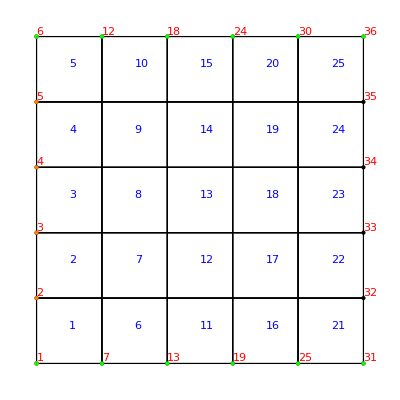

```mathematica
ClearAll[ShowNumbers,ShowBCs];
Options[PlotMeshBC]={ShowNumbers->True,ShowBCs->"DirichletBC"};
(*Options[PlotMeshBC]={ShowNumbers->True,ShowBCs->"NeumannBC"};*)
(*Options[PlotMeshBC]={ShowNumbers->True,ShowBCs->False};*)
PlotMeshBC[ShowNumbers->True]
```

### Newton solver

```mathematica
uMat=SparseArray[{},{Subscript[n, dof],Subscript[n, np]},0.0];
UMat=ReplacePart[uMat, DirichletNode];
ParallelEvaluate[rMat=SparseArray[{},{Subscript[n, dof]*Subscript[n, np]},0.0]];
ParallelMap[ComputeResidualMatrixU,Range[Subscript[n, el]]];
rMat=Plus@@(ParallelEvaluate@rMat);
Map[ApplyTraction,Edges];
Err =Norm[rMat[[IDno]],Infinity];
itr=0;
While[Err>10^-6&&itr++<MaxItr,
ParallelEvaluate[KMat=SparseArray[{},{Subscript[n, dof]*Subscript[n, np],Subscript[n, dof]*Subscript[n, np]},0.0]];
ParallelMap[ComputeStiffnessMatrixU,Range[Subscript[n, el]]];
KMat=Plus@@(ParallelEvaluate@KMat);
udsol=LinearSolve[KMat[[IDno,IDno]],rMat[[IDno]]];
udMat=SparseArray[{},{Subscript[n, dof]*Subscript[n, np]},0.0];
udMat[[IDno]]=udsol;
UMat+=Transpose[ArrayReshape[udMat,{Subscript[n, np],Subscript[n, dof]}]];
ParallelEvaluate[rMat=SparseArray[{},{Subscript[n, dof]*Subscript[n, np]},0.0]];
ParallelMap[ComputeResidualMatrixU,Range[Subscript[n, el]]];
rMat=Plus@@(ParallelEvaluate@rMat);
Map[ApplyTraction,Edges];
Err =Norm[rMat[[IDno]],Infinity];
Print["Iteration: ",itr,". \n Norm of residual for U : ",Err];
];
Print["Compute U Converged!"];
Ufvec=Table[ElementMeshInterpolation[{Ω^h}, UMat[[i,;;]]//Normal],{i,1,Subscript[n, dof]}];
```

Iteration: 1. 
 Norm of residual for U : 9.19403×10^-17

Compute U Converged!

### Stress Calculation

```mathematica
Subscript[n, ud]=Subscript[n, dof]*Subscript[n, dof];
ParallelEvaluate[aMat=SparseArray[{},{Subscript[n, np],Subscript[n, np]},0.0]];
ParallelEvaluate[UdMat=ConstantArray[0.0,{Subscript[n, np],Subscript[n, ud]}]];
ParallelMap[ComputeStressProjection,Range[Subscript[n, el]]];
aMat=Plus@@(ParallelEvaluate@aMat);
UdMat=Plus@@(ParallelEvaluate@UdMat);
SolUd=LinearSolve[aMat,UdMat];
SolUdMat=ArrayReshape[SolUd,{Length@SolUd,Subscript[n, dof],Subscript[n, dof]}];
StressMat=TensorContract[StiffnessContra⊗(SolUdMat+Transpose[SolUdMat,{1,3,2}])/2,{{3,6},{4,7}}];
StressMatf=ArrayReshape[ElementMeshInterpolation[{Ω^h},Flatten[StressMat,{1,2}][[#,;;]]] & /@ Range@Subscript[n, ud],{Subscript[n, dof],Subscript[n, dof]}];
```

### Plot Displacement 2D

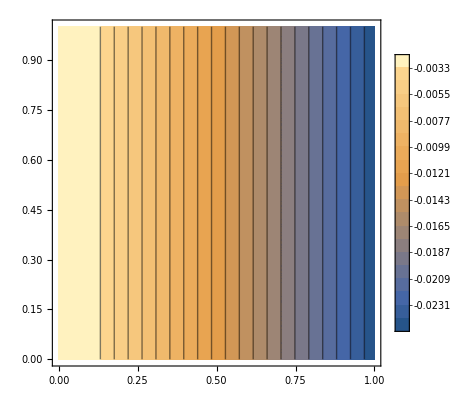

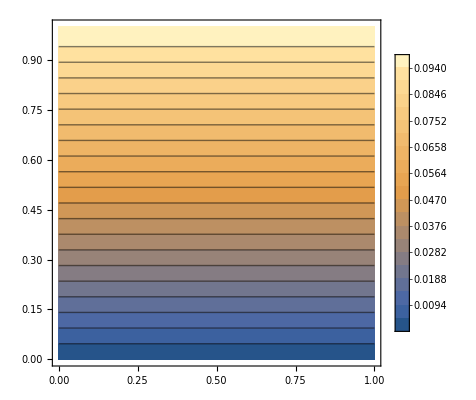

```mathematica
ContourPlot[Ufvec[[1]]@@{Subscript[x, 1],Subscript[x, 2]},{Subscript[x, 1],Subscript[x, 2]}∈Ω^h,PlotLegends->Automatic,PlotRange->All,Contours->20]
ContourPlot[Ufvec[[2]]@@{Subscript[x, 1],Subscript[x, 2]},{Subscript[x, 1],Subscript[x, 2]}∈Ω^h,PlotLegends->Automatic,PlotRange->All,Contours->20]
```

### Stress Plot in 2D

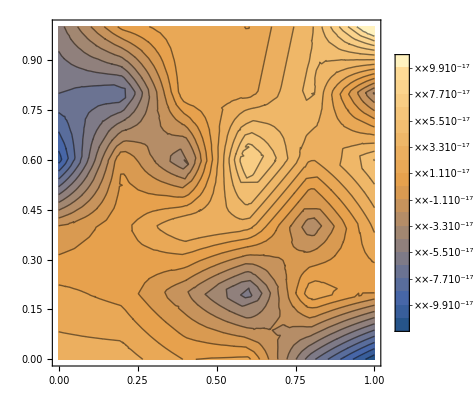

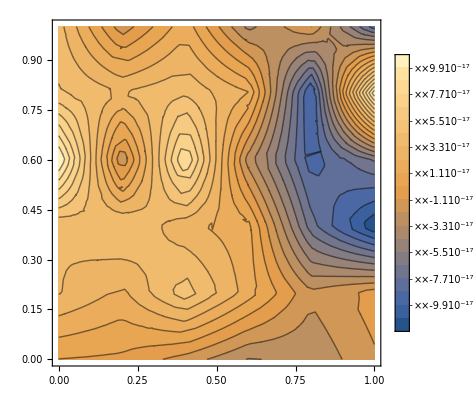

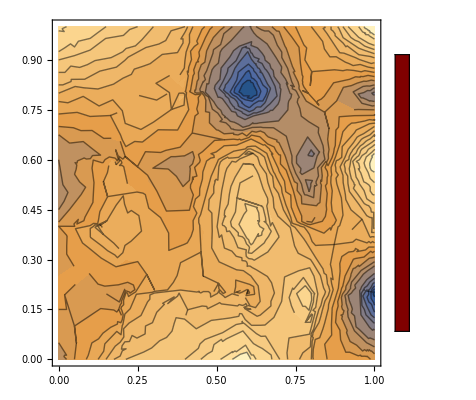

```mathematica
ContourPlot[StressMatf[[1,1]]@@{Subscript[x, 1],Subscript[x, 2]},{Subscript[x, 1],Subscript[x, 2]}∈Ω^h,PlotLegends->Automatic,PlotRange->All,Contours->20]
ContourPlot[StressMatf[[1,2]]@@{Subscript[x, 1],Subscript[x, 2]},{Subscript[x, 1],Subscript[x, 2]}∈Ω^h,PlotLegends->Automatic,PlotRange->All,Contours->20]
ContourPlot[StressMatf[[2,2]]@@{Subscript[x, 1],Subscript[x, 2]},{Subscript[x, 1],Subscript[x, 2]}∈Ω^h,PlotLegends->Automatic,PlotRange->All,Contours->20]
```

### Plot Displacement 3D

```mathematica
SliceContourPlot3D[Ufvec[[1]]@@{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]},Automatic,{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}∈Ω^h,PlotLegends->Automatic,PlotRange->All,Contours->20]
SliceContourPlot3D[Ufvec[[2]]@@{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]},"XStackedPlanes",{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}∈Ω^h,PlotLegends->Automatic,PlotRange->All,Contours->20]
SliceContourPlot3D[Ufvec[[3]]@@{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]},"XStackedPlanes",{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}∈Ω^h,PlotLegends->Automatic,PlotRange->All,Contours->20]
```

### Stress Plot in 3D

```mathematica
SliceContourPlot3D[StressMatf[[1,1]]@@{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]},Automatic,{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}∈Ω^h,PlotLegends->Automatic,PlotRange->All,Contours->20]
SliceContourPlot3D[StressMatf[[2,2]]@@{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]},"XStackedPlanes",{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}∈Ω^h,PlotLegends->Automatic,PlotRange->All,Contours->20]
SliceContourPlot3D[StressMatf[[1,2]]@@{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]},"XStackedPlanes",{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}∈Ω^h,PlotLegends->Automatic,PlotRange->All,Contours->20]
SliceContourPlot3D[StressMatf[[1,3]]@@{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]},"XStackedPlanes",{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}∈Ω^h,PlotLegends->Automatic,PlotRange->All,Contours->20]
SliceContourPlot3D[StressMatf[[2,3]]@@{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]},"XStackedPlanes",{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}∈Ω^h,PlotLegends->Automatic,PlotRange->All,Contours->20]
```